```mathematica
xml=Import[NotebookDirectory[]<>"~images\\"<>"E_1324_Rainbow6_even_target_diagonal.xml"];
{tfifile,volumefile,legends,face,imagefilenames,featurefilename,resultxml,imagefile,dataname,plotpath,imagepath}=xml;
Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]
```

C:\work\time-varying-visualization\colortf\Rainbow6_even.tfi
C:\_time_varying_data\supernova\E_1324.tif
{Feature 1,Feature 2,Feature 3,Feature 4,Feature 5,Feature 6}
left
{C:\work\time-varying-visualization\~images\E_1324_Rainbow6_even_target_diagonal_saliency_chart.pdf,C:\work\time-varying-visualization\~images\E_1324_Rainbow6_even_target_diagonal_visibility_chart.pdf,C:\work\time-varying-visualization\~images\E_1324_Rainbow6_even_target_diagonal_visibility_saliency_brightness_chart.pdf,C:\work\time-varying-visualization\~images\E_1324_Rainbow6_even_target_diagonal_visibility_saliency_saturation_chart.pdf,C:\work\time-varying-visualization\~images\E_1324_Rainbow6_even_target_diagonal_visibility_saliency_weighted_chart.pdf}
C:\work\time-varying-visualization\~images\E_1324_Rainbow6_even_target_diagonal_visibility_saliency_feature.png
C:\work\time-varying-visualization\~images\saliency.xml
C:\work\time-varying-visualization\~images\E_1324_Rainbow6_even_target_diagonal.png
E_1324_Rainbow6_even_target_diagonal
C:\work\time-varying-visualization\~plot\
C:\work\time-varying-visualization\~images\

```mathematica
time1=AbsoluteTime[];
```

```mathematica
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];

{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,ImageResize[d,ImageDimensions[d]/4]]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
{g1,g2}=ParallelMap[ImageResize[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]],ImageDimensions[d]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
index0=Flatten@Position[alpha0,_?(#>0&)];

CloseKernels[];
LaunchKernels[];
Clear[f];
Clear[data];
records={};
performance={};
epsilon=0.0001;
stepsize=0.05;
iterationcount1=64;
iterationcount2=32;
targets={ConstantArray[1./Length@index,Length@index],intensity0[[#]]&/@index0//#/Total[#]&,alpha0[[#]]&/@index0//#/Total[#]&};
target=targets[[2]];(* 1 even, 2 diagonal, 3 opacity as target *)
(*target={0.1,0.3,0.6}; (* manually specify targets: nucleon 0.1 0.3 0.6 vortex 1/3 1/3 1/3 *)*)
legends=MapIndexed["feature"<>ToString@First@#2&,index];
Length@features==Length@legends
```

True

Parameters for test data sets
nucleon_naive_proportional
22
3
tooth_naive	targets={0.1,0.3,0.6};
47
4
CT-Knee_naive	targets={0.1,0.3,0.6};
47
6
vortex_naive_proportional
39
18

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
VisibilityField[fun_]:=Module[{vis},
vis=Block[{f=fun,data=d},renderslices2[face]]
]
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
margin=4;
mrms=0;
mindex=0;
iteration=0;
exit=False;
t2=0;
t1=AbsoluteTime[];
list=Table[
If[exit,Nothing,
Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=Mean[(mean-target)^2];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
gradient=2*(mean-target);
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tfixed\t","converge\t",t2-t1,"\t",iterator,"\t",rms,"\t<",epsilon]];
If[rms<mrms || mrms==0,mrms=rms;mindex=iterator];
If[t2==0&&mindex+margin<iterator,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tfixed\t","diverge\t",t2-t1,"\t",iterator,"\t",rms,"\t",mindex,"\t",mrms]];
If[t2==0&&iterator==iterationcount1,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tfixed\t","max\t",t2-t1,"\t",iterator,"\t",rms]];
{mean,peaks0,rms,steps}
]
]
,{iterator,iterationcount1}];
```

E_1324_Rainbow6_even_target_diagonal	fixed	converge	350.863616	37	0.000084402	<0.0001

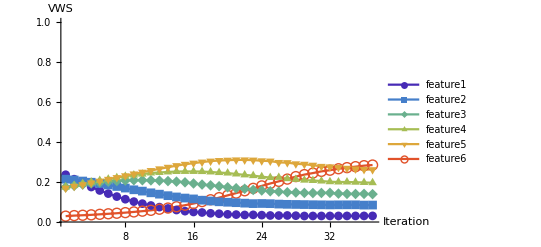

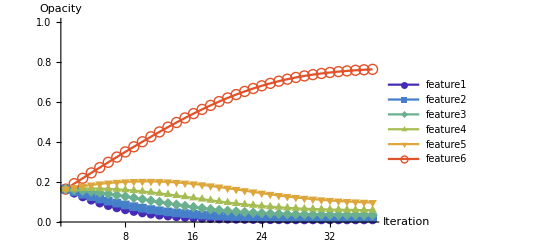

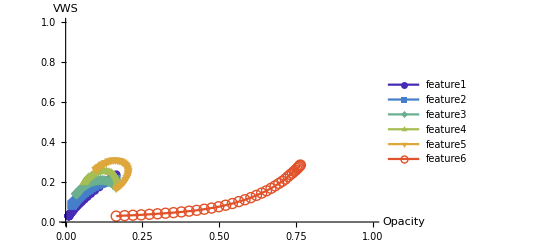

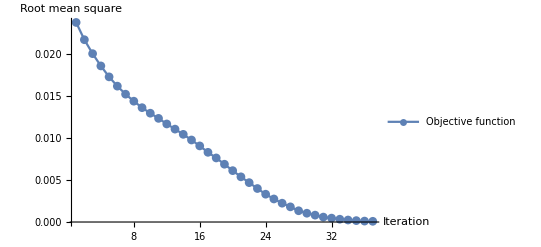

{350.863616,37,{0.0103505,0.0210626,0.0350791,0.0593675,0.0975283,0.764847},37,0.000084402}

```mathematica
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->None,PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iteration","VWS"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_saliency_fixed.pdf",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->None,PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iteration","Opacity"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_opacity_fixed.pdf",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->None,AxesLabel->{"Opacity","VWS"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic,BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_saliencyopacity_fixed.pdf",saliencyopacity1];
rmslist1=#3&@@@list;
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->None,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iteration","Root mean square"}]
Export[plotpath<>dataname<>"_rms_fixed.pdf",rms1];
path1=#2&@@@list;
minstep1=First@FirstPosition[rmslist1,_?(#==Min[rmslist1]&)];
AppendTo[records,{t2-t1,iteration,path1[[minstep1]],minstep1,rmslist1[[minstep1]]}];
AppendTo[performance,{t2-t1,iteration}];
{t2-t1,iteration,path1[[minstep1]],minstep1,rmslist1[[minstep1]]}
table1=TableForm[list,TableHeadings->{Automatic,{"VWS","Opacity", "Objective Function","Steps"}},TableSpacing->{2,1}];
Export[plotpath<>dataname<>"_table_fixed.pdf",table1];
```

```mathematica
(*(* Newton's method x(k+1)=x(k)-(f-f0)/(f'-f0') *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size (second order similar to Newton's) *)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient,direction,square},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
square:=(mean-target)^2;
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,g0,s0,dy,dx},
{rms0,mean0,p0,g0,s0}=previous;
dy=square-s0;
dx=gradient-g0;
If[Product[i,{i,dx}]≠0,direction=Normalize[dy/dx]*Norm[gradient];-direction*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks,gradient,square};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,iterationcount1}];
rmslist5=#3&@@@list;*)
```

```mathematica
(*rmslists1=ListLinePlot[{rmslist1,rmslist5},PlotLegends->{"Method 1","Method 2"},PlotLabel->None,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iteration","Objective function"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_rms_fixed_newton.pdf",rmslists1];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
margin=4;
mrms=0;
mindex=0;
iteration=0;
exit=False;
t2=0;
t1=AbsoluteTime[];
list=Table[
If[exit,Nothing,
Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex,minrms},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=If[Norm[previous]>0,minrms,Mean[(mean-target)^2]];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[Mean[(#-target)^2]&,meanlist];
minindex=First@Ordering[rmslist,1];
minrms=rmslist[[minindex]];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tparallelsearch\t","converge\t",t2-t1,"\t",iterator,"\t",rms,"\t<",epsilon]];
If[rms<mrms || mrms==0,mrms=rms;mindex=iterator];
If[t2==0&&mindex+margin<iterator,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tparallelsearch\t","diverge\t",t2-t1,"\t",iterator,"\t",rms,"\t",mindex,"\t",mrms]];
If[t2==0&&iterator==iterationcount2,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tparallelsearch\t","max\t",t2-t1,"\t",iterator,"\t",rms]];
{mean,peaks,rms,steps,multipliers[[minindex]]}
]
]
,{iterator,iterationcount2}];
```

E_1324_Rainbow6_even_target_diagonal	parallelsearch	converge	92.9980619	5	0.0000586727	<0.0001

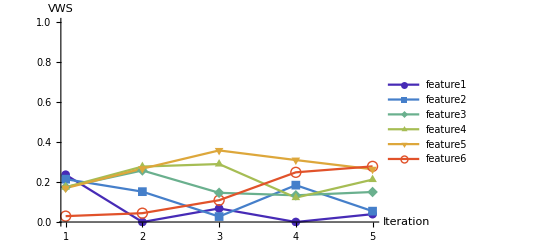

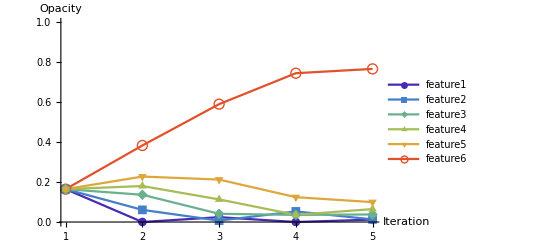

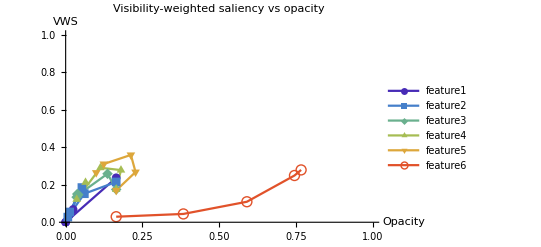

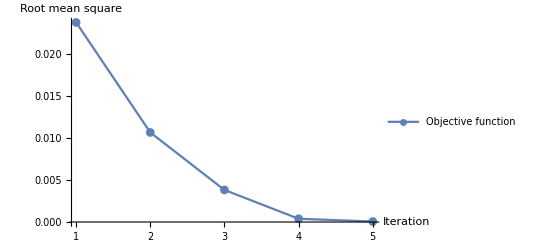

{92.9980619,5,{0.0121212,0.0131256,0.037891,0.0647504,0.099636,0.767212},5,0.0000586727}

```mathematica
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->None,PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iteration","VWS"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_saliency_parallelsearch.pdf",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->None,PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iteration","Opacity"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_opacity_parallelsearch.pdf",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","VWS"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic,BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_saliencyopacity_parallelsearch.pdf",saliencyopacity2];
rmslist2=#3&@@@list;
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->None,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iteration","Root mean square"}]
Export[plotpath<>dataname<>"_rms_parallelsearch.pdf",rms2];
path2=#2&@@@list;
minstep2=First@FirstPosition[rmslist2,_?(#==Min[rmslist2]&)];
AppendTo[records,{t2-t1,iteration,path2[[minstep2]],minstep2,rmslist2[[minstep2]]}];
AppendTo[performance,{t2-t1,iteration}];
{t2-t1,iteration,path2[[minstep2]],minstep2,rmslist2[[minstep2]]}
table2=TableForm[list,TableHeadings->{Automatic,{"VWS","Opacity", "Objective Function","Steps","Multiplier(γ)"}},TableSpacing->{2,1}];
Export[plotpath<>dataname<>"_table_parallelsearch.pdf",table2];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
margin=4;
mrms=0;
mindex=0;
iteration=0;
exit=False;
t2=0;
t1=AbsoluteTime[];
list=Table[
If[exit,Nothing,
Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=If[Norm[previous]>0,minrms,Mean[(mean-target)^2]];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=Mean[(minmean-target)^2];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=Mean[(mean2-target)^2];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tlinesearch\t","converge\t",t2-t1,"\t",iterator,"\t",rms,"\t<",epsilon]];
If[rms<mrms || mrms==0,mrms=rms;mindex=iterator];
If[t2==0&&mindex+margin<iterator,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tlinesearch\t","diverge\t",t2-t1,"\t",iterator,"\t",rms,"\t",mindex,"\t",mrms]];
If[t2==0&&iterator==iterationcount2,t2=AbsoluteTime[];iteration=iterator;exit=True;Print[dataname,"\tlinesearch\t","max\t",t2-t1,"\t",iterator,"\t",rms]];
{mean,peaks,rms,steps,multipliers[[minindex]]}
]
]
,{iterator,iterationcount2}];
```

E_1324_Rainbow6_even_target_diagonal	linesearch	converge	196.803321	5	0.0000968075	<0.0001

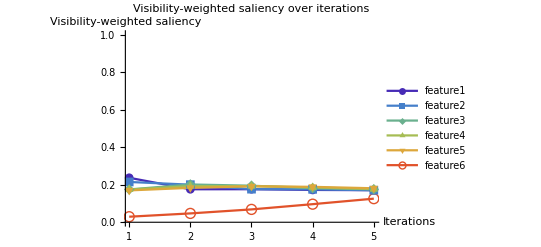

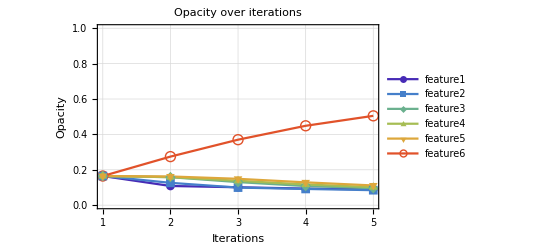

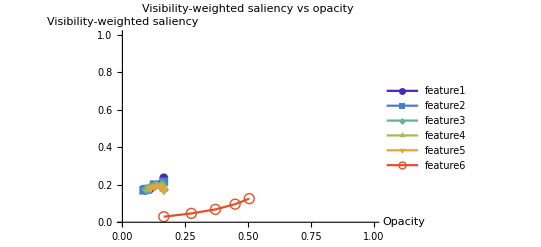

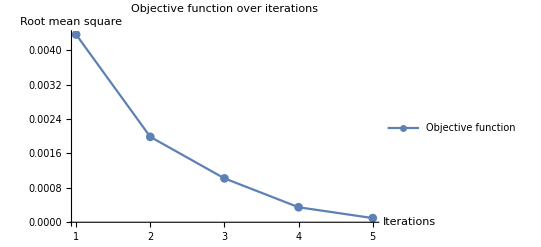

{196.803321,5,{0.0893597,0.0847138,0.0960339,0.101824,0.111391,0.504913},5,0.0000968075}

```mathematica
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->legends,PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_linesearch.pdf",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->legends,PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"},BaseStyle->{FontSize->14},PlotTheme->"Detailed"]
Export[plotpath<>dataname<>"_opacity_linesearch.pdf",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->legends,PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_linesearch.pdf",saliencyopacity3];
rmslist3=#3&@@@list;
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_linesearch.pdf",rms3];
path3=#2&@@@list;
minstep3=First@FirstPosition[rmslist3,_?(#==Min[rmslist3]&)];
AppendTo[records,{t2-t1,iteration,path3[[minstep3]],minstep3,rmslist3[[minstep3]]}];
AppendTo[performance,{t2-t1,iteration}];
{t2-t1,iteration,path3[[minstep3]],minstep3,rmslist3[[minstep3]]}
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Objective Function","Steps","Multiplier(γ)"}},TableSpacing->{2,1}];
Export[plotpath<>dataname<>"_table_linesearch.pdf",table3];
```

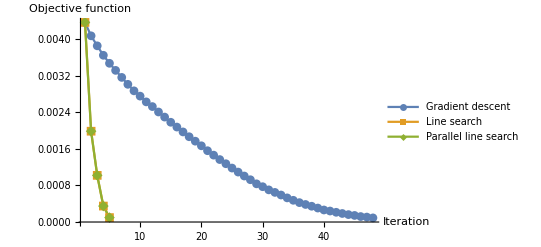

```mathematica
rmslists2=ListLinePlot[{rmslist1,rmslist2,rmslist3},PlotLegends->{"Gradient descent","Line search","Parallel line search"},PlotLabel->None,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iteration","Objective function"},BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_rms_fixed_linesearch_parallel.pdf",rmslists2];
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xmlobject},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xmlobject=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function created using Wolfram Mathematica"]},VoreenData,{}];
Export[filename,xmlobject, "XML"];
rgbafunction2
];
```

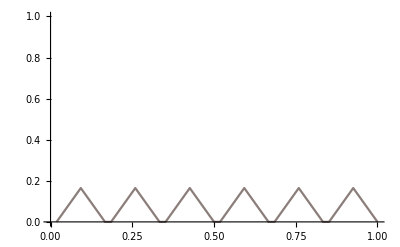

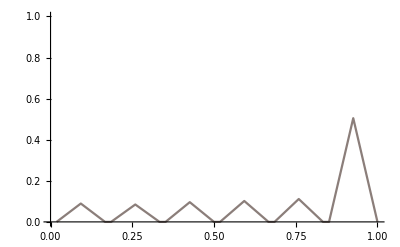

```mathematica
tf1=saveTransferFunction[path1[[minstep1]],plotpath<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[path2[[minstep2]],plotpath<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[path3[[minstep3]],plotpath<>dataname<>"_optimized_linesearch.tfi"];
(*tf5=saveTransferFunction[path5[[minstep5]],plotpath<>dataname<>"_optimized_newton.tfi"];*)

Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]];
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]];
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

```mathematica
(*tfifile
tfi=plotpath<>dataname<>"_optimized_parallelsearch.tfi"
Run["D:/voreenve-4.4-win64/voreentool.exe -w \"D:/document/work/time-varying-visualization/nucleon_features_views.vws\" --script \"D:/document/work/time-varying-visualization/2dfs_optimization.py\" --opengl --run-event-loop"];*)
```

```mathematica
Prepend[performance,dataname]//TableForm
```

E_1324_Rainbow6_even_target_diagonal | 
457.6723397 | 48
93.7527401 | 5
196.803321 | 5

2016-08-19 2016-08-23

1 thread
"nucleon_naive_proportional" | ""
1.092109 | 17
1.064106 | 2
0.5740574 | 2

"nucleon_naive_proportional" | ""
1.073611 | 17
0.9560956 | 2
0.5780578 | 2

"tooth_naive_proportional" | ""
7.7180177 | 21
3.7126731 | 2
3.335925 | 2

"tooth_naive_proportional" | ""
7.5504484 | 21
3.525623 | 2
3.244821 | 2

"CT-Knee_naive_proportional" | ""
33.697512 | 17
17.722395 | 2
17.753028 | 2

"CT-Knee_naive_proportional" | ""
35.082188 | 17
18.441684 | 2
18.546231 | 2

"vortex_naive_proportional" | ""
13.628541 | 33
24.365739 | 13
15.371 | 13

"vortex_naive_proportional" | ""
14.440962 | 33
24.10195 | 13
15.59 | 13

2 threads
"nucleon_naive_proportional" | ""
1.046608 | 17
0.4306051 | 2
0.5460035 | 2

"nucleon_naive_proportional" | ""
1.031023 | 17
0.4212027 | 2
0.5890516 | 2

"tooth_naive_proportional" | ""
7.505276 | 21
2.057023 | 2
3.263801 | 2

"tooth_naive_proportional" | ""
7.5172077 | 21
2.310231 | 2
3.29733 | 2

"CT-Knee_naive_proportional" | ""
35.001281 | 17
11.85593 | 2
17.765353 | 2

"CT-Knee_naive_proportional" | ""
33.660687 | 17
11.586312 | 2
17.769171 | 2

"vortex_naive_proportional" | ""
13.9964 | 33
13.4183 | 13
15.5087 | 13

"vortex_naive_proportional" | ""
13.681288 | 33
13.759288 | 13
15.5689 | 13

4 threads
"nucleon_naive_proportional" | ""
1.311635 | 17
0.4528263 | 2
0.6089733 | 2

"nucleon_naive_proportional" | ""
1.1388 | 17
0.3276 | 2
0.6084 | 2

"tooth_naive_proportional" | ""
7.5717571 | 21
1.710171 | 2
3.240324 | 2

"tooth_naive_proportional" | ""
7.6472 | 21
1.7918 | 2
3.2982 | 2

"CT-Knee_naive_proportional" | ""
35.6985695 | 17
9.7139713 | 2
18.023309 | 2

"CT-Knee_naive_proportional" | ""
34.451 | 17
9.064 | 2
18.2654 | 2

"vortex_naive_proportional" | ""
14.195193 | 33
8.8844652 | 13
15.350096 | 13

"vortex_naive_proportional" | ""
13.780894 | 33
9.2247254 | 13
15.105661 | 13

8 threads
"nucleon_naive_proportional" | ""
1.061117 | 17
0.3930174 | 2
0.6060533 | 2

"nucleon_naive_proportional" | ""
1.086109 | 17
0.3630363 | 2
0.5820582 | 2

"tooth_naive_proportional" | ""
7.6017601 | 21
1.508319 | 2
3.270247 | 2

"tooth_naive_proportional" | ""
7.5086559 | 21
1.623024 | 2
3.226622 | 2

"CT-Knee_naive_proportional" | ""
33.848443 | 17
8.5419817 | 2
17.868918 | 2

"CT-Knee_naive_proportional" | ""
33.839322 | 17
9.9799238 | 2
17.752775 | 2

"vortex_naive_proportional" | ""
13.754319 | 33
8.395803 | 13
14.85949 | 13

"vortex_naive_proportional" | ""
14.242891 | 33
8.4084539 | 13
15.5845 | 13

```mathematica
recordxml=plotpath<>"records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

E_1324_Rainbow6_even_target_diagonal→{{457.6723397,48,{0.0864267,0.0814773,0.0900605,0.0945071,0.0994851,0.536279},48,0.0000904853},{93.7527401,5,{0.0893597,0.0847138,0.0960339,0.101824,0.111391,0.504913},5,0.0000968075},{196.803321,5,{0.0893597,0.0847138,0.0960339,0.101824,0.111391,0.504913},5,0.0000968075}}

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Line search"},{"Parallel line search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec,BaseStyle->{FontSize->14}]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec,BaseStyle->{FontSize->14}]
Export[plotpath<>dataname<>"_parameterspace.pdf",sp];
Export[plotpath<>dataname<>"_parameterspace_path.pdf",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
(*densityplots=MapIndexed[Show[#,PlotLabel->"VWS of feature "<>ToString[First@#2],ViewPoint->vec,BaseStyle->{FontSize->14}]&,dplots]*)
densityplots=MapIndexed[Show[#,PlotLabel->"",ViewPoint->vec,BaseStyle->{FontSize->14}]&,dplots]
MapIndexed[Export[plotpath<>dataname<>"_densityplot"<>ToString[First@#2]<>".pdf",#]&,densityplots];*)
```

```mathematica
{path1[[minstep1]],path2[[minstep2]],path3[[minstep3]]}//TableForm[#,TableHeadings->{Automatic, legends}]&
```

| feature1 | feature2 | feature3 | feature4 | feature5 | feature6
1 | 0.0864267 | 0.0814773 | 0.0900605 | 0.0945071 | 0.0994851 | 0.536279
2 | 0.0893597 | 0.0847138 | 0.0960339 | 0.101824 | 0.111391 | 0.504913
3 | 0.0893597 | 0.0847138 | 0.0960339 | 0.101824 | 0.111391 | 0.504913

```mathematica
(* measure computation time *)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
VisibilitySaliency[path1[[minstep1]]]//AbsoluteTiming
Visibility[fun]//AbsoluteTiming
VisibilityField[fun]//AbsoluteTiming*)
```

```mathematica
(*Table[VisibilitySaliency[path1[[minstep1]]]//AbsoluteTiming,{i,10}]//Mean@First@Transpose[#]&*)
```

```mathematica
(*(* generate transfer functions for optimization with different rms thresholds *)
Table[Module[{index,tf0},
index=First@FirstPosition[rmslist1,_?(#<rmsthreshold&)];
tf0=saveTransferFunction[path1[[index]],NotebookDirectory[]<>"rms_threshold\\"<>dataname<>"_optimized_fixed_"<>ToString[rmsthreshold]<>".tfi"];
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"rms<"<>ToString[rmsthreshold],PlotTheme->"Detailed"]
],{rmsthreshold,{0.1,0.09,0.08,0.07,0.06,0.05,0.04,0.03,0.02,0.01}}]*)
```

```mathematica
time2=AbsoluteTime[];
time2-time1
```

854.771637